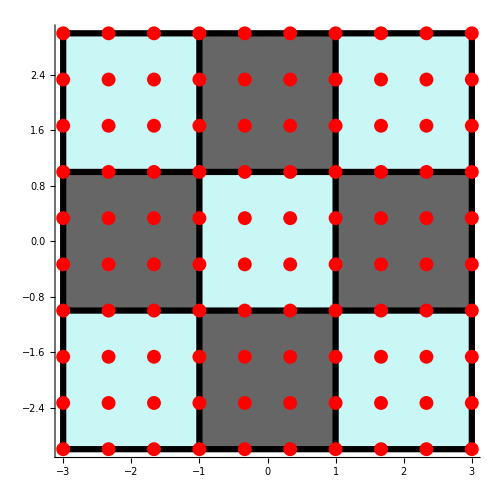

```mathematica
layout2d=Graphics[
	{
		RGBColor["#a4f2f1"], Opacity[0.6],
		lightSquares,
		Black,
		darkSquares,
		Thickness[0.009],Opacity[1.0],
		lines,
		Red,PointSize[0.02],
		Point[Flatten[nodes,1]]
	},
	Axes->True,
	AxesOrigin->{-3.2,-3.2},
	AxesStyle->Directive[26, Black],
	ImageSize->500
]
```

```mathematica
Export["layout2d.png", layout2d,ImageResolution->90]
```

layout2d.png

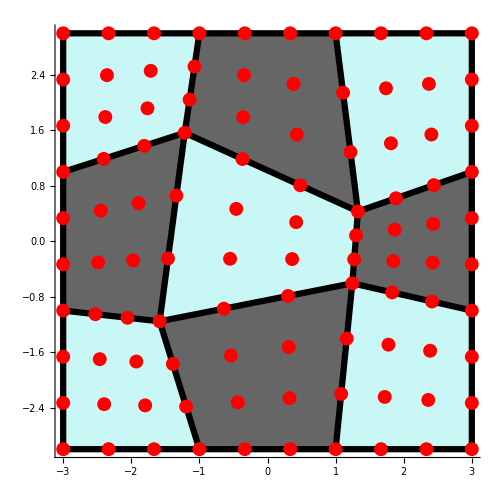

```mathematica
layout2dTrans=Graphics[
	{
		RGBColor["#a4f2f1"], Opacity[0.6],
		transLightSquares,
		Black,Thickness[0.009],
		transDarkSquares,
		Opacity[1],
		transLines,
		Red,PointSize[0.02],
		Point[Flatten[transNodes,1]]
	},
	Axes->True,
	AxesOrigin->{-3.2,-3.2},
	AxesStyle->Directive[26, Black],
	ImageSize->500
]
```

```mathematica
Export["layout2dTrans.png", layout2dTrans,ImageResolution->90]
```

layout2dTrans.png